# Matrices P, Q, V and W

## https://arxiv.org/abs/2104.05122 Script to generate pictures used in PhD thesis of WB. Please avoid direct copying of these pictures without permission, as it will explicitly clash with already published work; name[at]uj.edu.pl name = w.bruzda

```mathematica
ResourceFunction["MaTeXInstall"][]
```

```mathematica
(* customized path (I use m$win only at the workplace...) *)
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs9.54.0\\bin\\gswin64c.exe"]
```

```mathematica
ConfigureMaTeX[]
```

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x^{11}"]
```

-Graphics-

```mathematica
S=ArrayFlatten[Transpose[ArrayReshape[IdentityMatrix[36],{6,6,6,6}],{3,1,2,4}]];

T2[a_]:=Module[{dim,sdim,ret}, (* partial transpose X^Subscript[T, 2] - courtesy of GRM *)
dim=Dimensions[a]⟦1⟧;
sdim=Sqrt[dim];
ret=Partition[a,{sdim,sdim}];
ret=Map[Transpose,ret,{2}];
ret=ArrayFlatten[ret];
Return[ret];
];

(* R2[M_]:=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}] *)
RF[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}];
Return[ret]
];

Xi[M_]:=1/3(M+RF[T2[M]]+T2[RF[M]]);

SL[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=d^2/(d^2-1)(1-Total[Eigenvalues[M.M†]^2]/Tr[M.M†]^2);
Return[ret];
]

ep[M_]:=(SL[RF[M]]+SL[RF[M.S]]-1)//N
gt[M_]:=(SL[RF[M]]-SL[RF[M.S]]+1)//N
```

## Matrix CNot

```mathematica
CNot={
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}};
```

## Matrix P_36 = \tilde{P} (by Clarisse et al.) (2005)

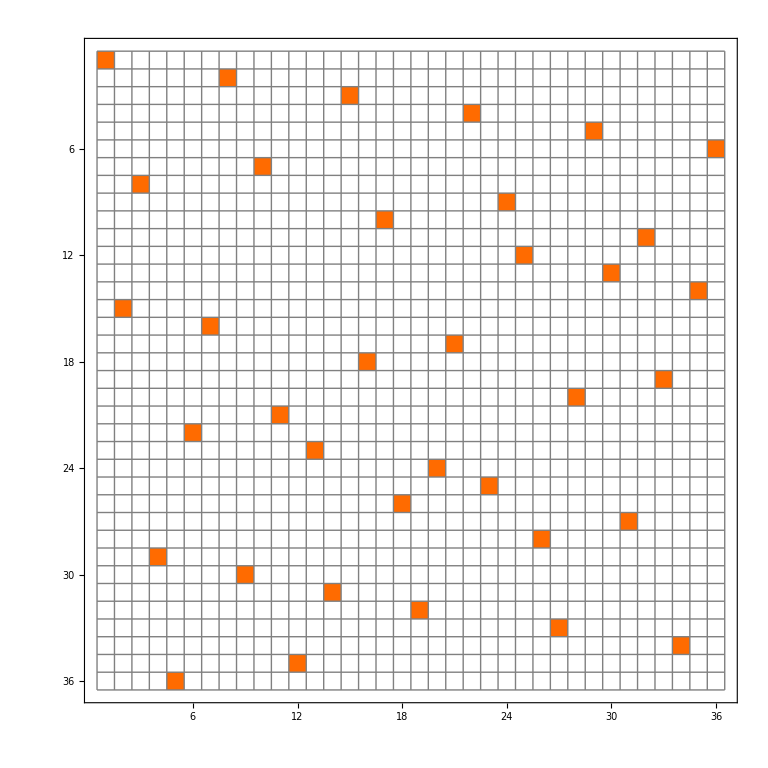

True

0.996825

0.996825

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{√2,√2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
(* Subscript[P, 36] in explicit form *)
P36={
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[P36]
OrthogonalMatrixQ[P36]
ep[P36]
%//N
SingularValueList/@{#,RF@#,T2@#}&[P36]
```

```mathematica
P36FromAnotherSourceToConfirmOnesOccupyCorrectPlaces={{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}};
MatrixPlot[Unitize[P36FromAnotherSourceToConfirmOnesOccupyCorrectPlaces]-Unitize[P36],Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}}]
```

-Graphics-

```mathematica
(* different form of Subscript[P, 36] *)
PVector={1,15,8,29,36,22,16,2,30,7,21,35,23,31,3,18,10,26,32,24,17,4,25,9,12,28,33,20,5,13,27,11,19,34,14,6};
P36V=SparseArray[Transpose[{PVector,Range[36]}]->1];
MatrixForm[P36V];
OrthogonalMatrixQ[P36V]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[P36V]
ep[P36V]
%//N
SingularValueList/@{P36V,RF@P36V,T2@P36V}
```

True

-Graphics-

0.996825

0.996825

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{√2,√2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

## Matrix Q_36 (once it was B_36) (2017-10-12) -- first improvement of P_36

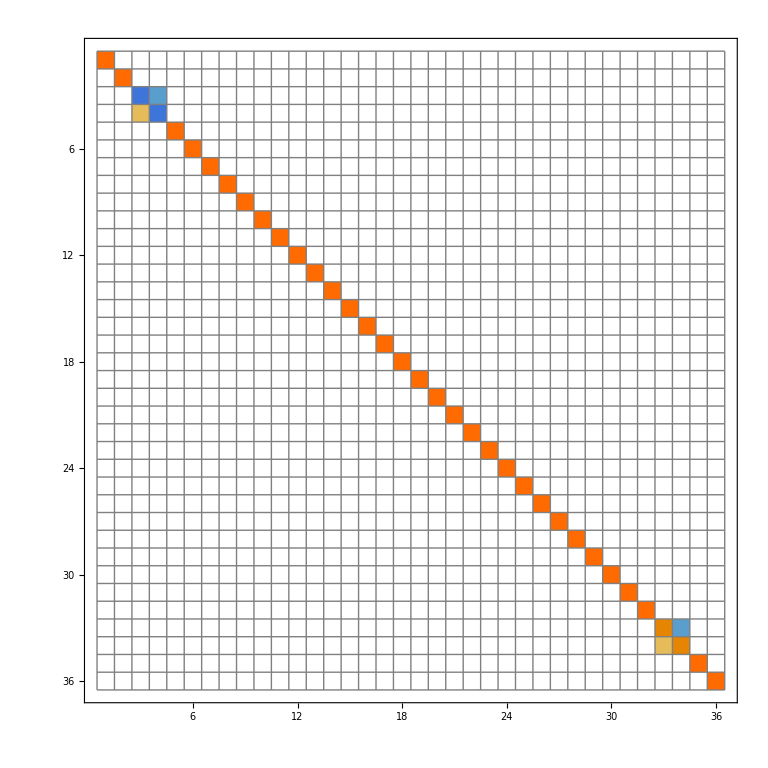

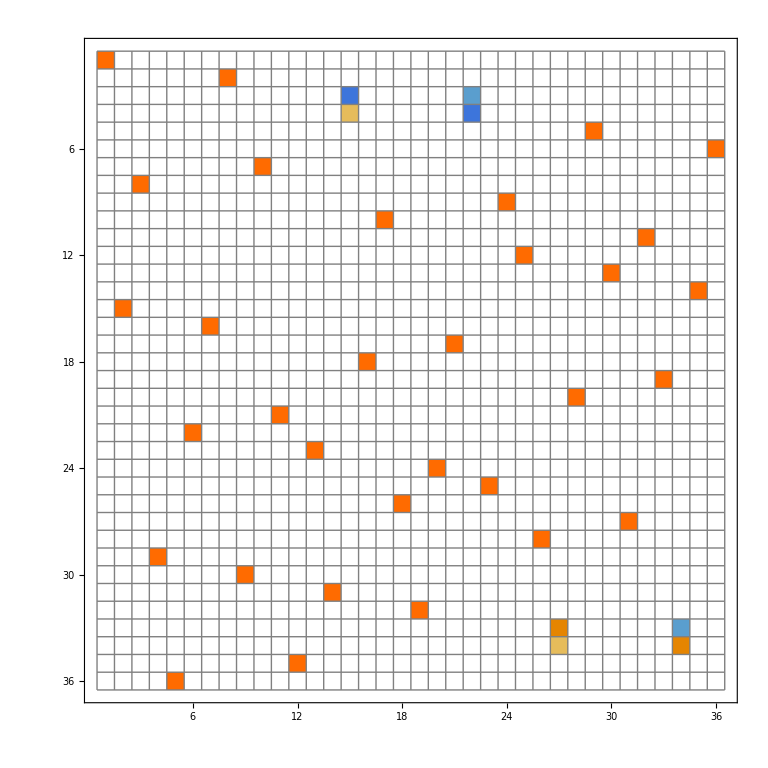

True

True

0.997619

0.997619

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{√(3/2),√(3/2),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1/(√2),1/(√2)},{√(3/2),√(3/2),√(3/2),√(3/2),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1/(√2),1/(√2),1/(√2),1/(√2)}}

```mathematica
p=π{ 5/6,1/6};
Q0=ArrayFlatten[{
{IdentityMatrix[2],0,0,0,0},
{0,RotationMatrix[p[[1]]],0,0,0},
{0,0,IdentityMatrix[28],0,0},
{0,0,0,RotationMatrix[p[[2]]],0},
{0,0,0,0,IdentityMatrix[2]}
}];
Q=Q0.P36;
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[Q0]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[Q]
OrthogonalMatrixQ[Q]
OrthogonalMatrixQ[Q0]
ep[Q]
%//N
SingularValueList/@{#,RF@#,T2@#}&[Q]
```

```mathematica
(* quick check *)
SL[T2@Q]//Simplify
36/35(1-Total[Eigenvalues[T2@Q.ConjugateTranspose[T2@Q]]^2]/Tr[T2@Q.ConjugateTranspose[T2@Q]]^2)
```

629/630

629/630

## Matrix V=V^*= V_36(p_1, p_2, ..., p_18) (2018-11-01) -- improvement of Q_36 (once B_36)

{36,36}

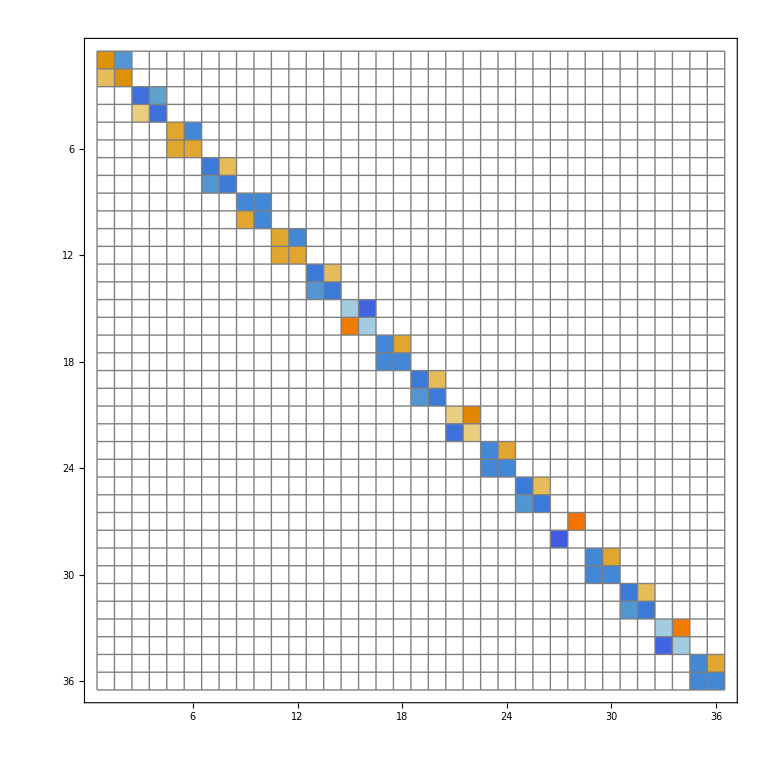

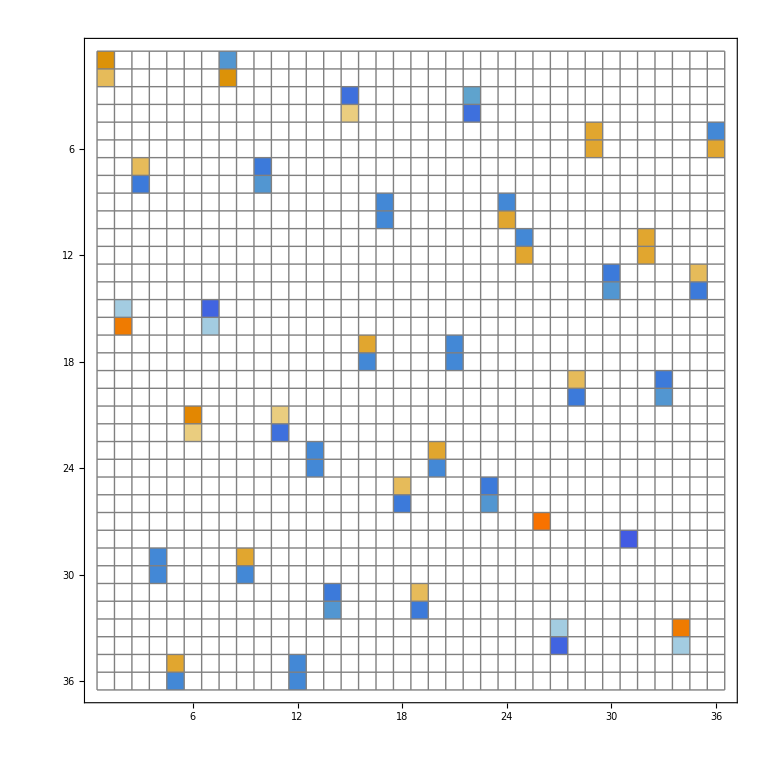

True

True

0.998724

0.998724

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3)))},{√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3)))}}

```mathematica
(*p=Pi{1/3,1/4,1/5,4/3,1/6,6/5,1/3,0,1/5,1/3,1/12,6/5,1/3,11/12,1/5,1/3,5/6,6/5};*)
p=π{1/5,5/6,1/4,6/5,3/4,1/4,6/5,7/12,5/4,6/5,5/3,5/4,6/5,3/2,5/4,6/5,17/12,5/4};
V0=ArrayFlatten[{
{RotationMatrix[p[[1]]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,RotationMatrix[p[[2]]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,RotationMatrix[p[[3]]],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,RotationMatrix[p[[4]]],0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,RotationMatrix[p[[5]]],0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,RotationMatrix[p[[6]]],0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,RotationMatrix[p[[7]]],0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,RotationMatrix[p[[8]]],0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,RotationMatrix[p[[9]]],0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,RotationMatrix[p[[10]]],0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[11]]],0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[12]]],0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[13]]],0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[14]]],0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[15]]],0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[16]]],0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[17]]],0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[18]]]}
}];
Dimensions[V0]
V=V0.P36;
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[V0]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[V]
OrthogonalMatrixQ[V]
OrthogonalMatrixQ[V0]
ep[V]
%//N
SingularValueList/@{#,RF@#,T2@#}&[V]
```

## Matrix W_5 (reduced form of V_36)

{36,36}

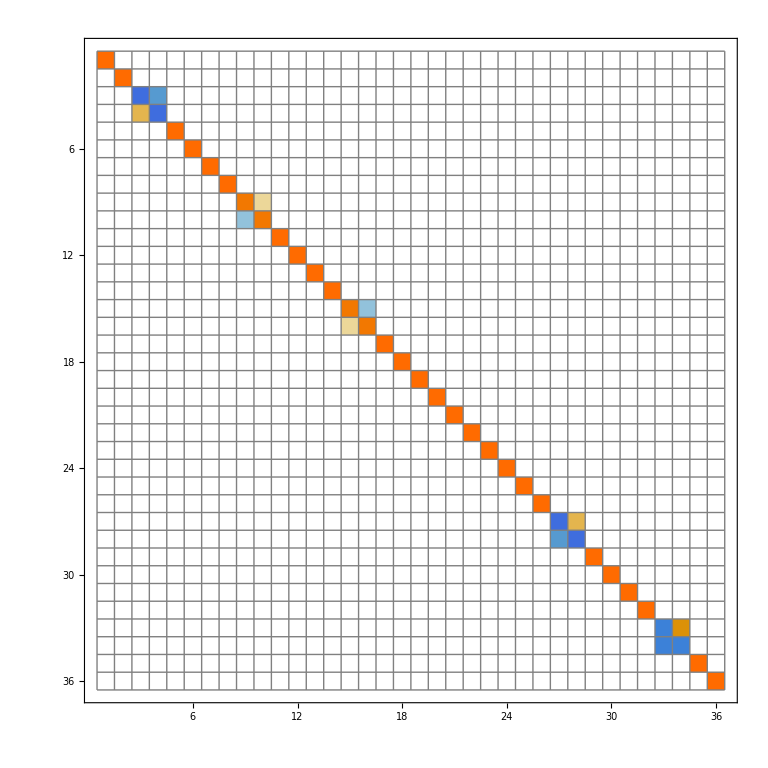

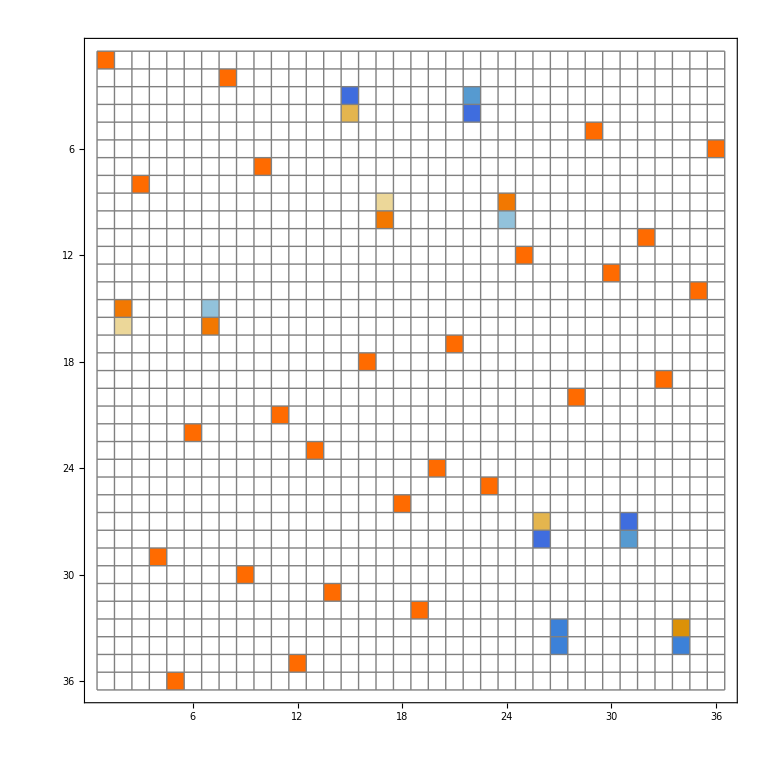

True

True

0.998724

1.

1.

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3)))},{√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),√(1/2 (2+√(2-√3))),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3))),√(1/2 (2-√(2-√3)))}}

```mathematica
p=π{5/6,23/12,1/12,0,7/6,5/4};
W0=ArrayFlatten[{
{IdentityMatrix[2],0,0,0,0,0,0,0,0,0,0,0,0},
{0,RotationMatrix[p[[1]]],0,0,0,0,0,0,0,0,0,0,0},
{0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0,0,0},
{0,0,0,RotationMatrix[p[[2]]],0,0,0,0,0,0,0,0,0},
{0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0},
{0,0,0,0,0,RotationMatrix[p[[3]]],0,0,0,0,0,0,0},
{0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0},
{0,0,0,0,0,0,0,RotationMatrix[p[[4]]],0,0,0,0,0},
{0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0},
{0,0,0,0,0,0,0,0,0,RotationMatrix[p[[5]]],0,0,0},
{0,0,0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0},
{0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[p[[6]]],0},
{0,0,0,0,0,0,0,0,0,0,0,0,IdentityMatrix[2]}
}];
Dimensions[W0]
W=W0.P36;
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[W0]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[W]
OrthogonalMatrixQ[W]
OrthogonalMatrixQ[W0]
ep[W]
gt[W]
%//N
SingularValueList/@{#,RF@#,T2@#}&[W]
```

```mathematica
(* different representations of roots for svd(W) *)
N[{1/2 √(4-√2+√6),√((2+√(2-√3))/2)},20]
N[{1/2 √(4+√2-√6),√((2-√(2-√3))/2)},20]
```

{1.1219710535938620027,1.1219710535938620027}

{0.8609186691537588196,0.8609186691537588196}

## Trajectories connecting P, Q and W (V)

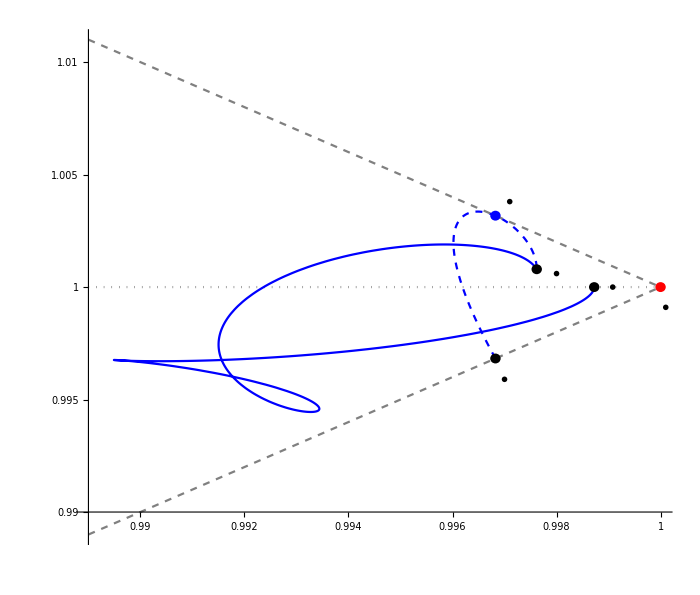

```mathematica
ω1[t_]:=π t{5/6,1/6};
MQ[ω_]:=ArrayFlatten[{
{IdentityMatrix[2],0,0,0,0},
{0,RotationMatrix[ω[[1]]],0,0,0},
{0,0,IdentityMatrix[28],0,0},
{0,0,0,RotationMatrix[ω[[2]]],0},
{0,0,0,0,IdentityMatrix[2]}
}].P36;
ω2[t_]:=π/12{10, t 23,t,0, t 14,2+13t };
MW[ω_]:=ArrayFlatten[{
{IdentityMatrix[2],0,0,0,0,0,0,0,0,0,0,0,0},
{0,RotationMatrix[ω[[1]]],0,0,0,0,0,0,0,0,0,0,0},
{0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0,0,0},
{0,0,0,RotationMatrix[ω[[2]]],0,0,0,0,0,0,0,0,0},
{0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0},
{0,0,0,0,0,RotationMatrix[ω[[3]]],0,0,0,0,0,0,0},
{0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0},
{0,0,0,0,0,0,0,RotationMatrix[ω[[4]]],0,0,0,0,0},
{0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0},
{0,0,0,0,0,0,0,0,0,RotationMatrix[ω[[5]]],0,0,0},
{0,0,0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0},
{0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[ω[[6]]],0},
{0,0,0,0,0,0,0,0,0,0,0,0,IdentityMatrix[2]}
}].P36;
x0=0.989;
ParametricPlot[
{
{(1-x)x0+x,1},
{ep[MQ[ω1[x]]],gt[MQ[ω1[x]]]},
{ep[MW[ω2[x]]],gt[MW[ω2[x]]]},
{(1-x)x0+x,(1-x)x0+x},
{(1-x)x0+x,(1-(-x+2))x0+(-x+2)}
},
{x,0,1},
AspectRatio->0.85,
AxesOrigin->{x0,0.99},
Ticks->{{0.99,0.992,0.994,0.996,0.998,1},{0,985,0.990,0.995,1,1.005,1.010,1.015}},
BaseStyle->{FontFamily->"Latin",FontSize->22},
AxesLabel->{MaTeX["e_p",FontSize->24],MaTeX["g_t",FontSize->24]},
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
PlotStyle->{Directive[Dotted, Gray],Directive[Dashed,Blue],Blue,Directive[Dashed,Gray],Directive[Dashed,Gray]},
Epilog->{
{Black,Disk[{ep[P36],gt[P36]},{.0001,.00022}]},
{Black,Disk[{ep[Q],gt[Q]},{.0001,.00022}]},
{Black,Disk[{ep[V],gt[V]},{.0001,.00022}]},
{Blue,Disk[{ep[P36.S],gt[P36.S]},{.0001,.00022}]},
{Red,Disk[{1,1},{.0001,.00022}]},
Style[Text[Style[MaTeX["P",FontSize->22]],{0.9970,0.9959}],Black,16],
Style[Text[Style[MaTeX["PS",FontSize->22]],{0.9971,1.0038}],Black,16],
Style[Text[Style[MaTeX["Q^{\star}",FontSize->22]],{0.998,1.0006}],Black,16],
Style[Text[Style[MaTeX["W",FontSize->22]],{0.99908,1}],Black,16],
Style[Text[Style[MaTeX["T_{36}",FontSize->22]],{1.0001,0.9991}],Black,16]
},
ImageSize->700
]
```

## Other general trajectories

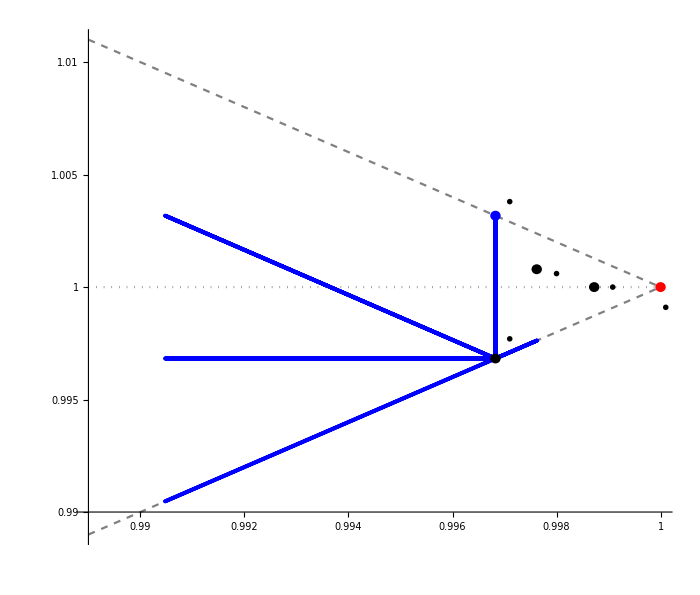

```mathematica
ω1[t_]:=π {t, t,0,0,-t,-t};
ω2[t_]:=π {t,-t,-t,-t,-t,-t};
ω3[t_]:=π {t, t,t,-t,-t,-t};
ω4[t_]:=π {-t, t,t,t,t,-t};
MW[ω_]:=ArrayFlatten[{
{IdentityMatrix[2],0,0,0,0,0,0,0,0,0,0,0,0},
{0,RotationMatrix[ω[[1]]],0,0,0,0,0,0,0,0,0,0,0},
{0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0,0,0},
{0,0,0,RotationMatrix[ω[[2]]],0,0,0,0,0,0,0,0,0},
{0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0,0,0},
{0,0,0,0,0,RotationMatrix[ω[[3]]],0,0,0,0,0,0,0},
{0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0,0,0},
{0,0,0,0,0,0,0,RotationMatrix[ω[[4]]],0,0,0,0,0},
{0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0,0,0},
{0,0,0,0,0,0,0,0,0,RotationMatrix[ω[[5]]],0,0,0},
{0,0,0,0,0,0,0,0,0,0,IdentityMatrix[4],0,0},
{0,0,0,0,0,0,0,0,0,0,0,RotationMatrix[ω[[6]]],0},
{0,0,0,0,0,0,0,0,0,0,0,0,IdentityMatrix[2]}
}].P36;
ParametricPlot[
{
{(1-x)0.989+x,1},
{(1-x)0.989+x,(1-x)0.989+x},
{(1-x)0.989+x,(1-(-x+2))0.989+(-x+2)},
{ep[MW[ω1[x]]],gt[MW[ω1[x]]]},
{ep[MW[ω2[x]]],gt[MW[ω2[x]]]},
{ep[MW[ω3[x]]],gt[MW[ω3[x]]]},
{ep[MW[ω4[x]]],gt[MW[ω4[x]]]}
},
{x,0,1},
AspectRatio->0.85,
AxesOrigin->{0.989,0.99},
BaseStyle->{FontFamily->"Latin",FontSize->22},
AxesLabel->{MaTeX["e_p",FontSize->24],MaTeX["g_t",FontSize->24]},
Ticks->{{0.990,0.992,0.994,0.996,0.998,1},{0,985,0.990,0.995,1,1.005,1.010,1.015}},
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
PlotStyle->{
Directive[Dotted,Gray],
Directive[Dashed,Gray],Directive[Dashed,Gray],
Directive[Thickness[.004],Blue],
Directive[Thickness[.004],Blue],
Directive[Thickness[.004],Blue],
Directive[Thickness[.004],Blue]},(* watch the order of plotting, to control overlay *)
Epilog->{
{Black,Disk[{ep[P36],gt[P36]},{.0001,.00022}]},
{Black,Disk[{ep[Q],gt[Q]},{.0001,.00022}]},
{Black,Disk[{ep[V],gt[V]},{.0001,.00022}]},
{Red,Disk[{1,1},{.0001,.00022}]},
{Blue,Disk[{ep[P36.S],gt[P36.S]},{.0001,.00022}]},
Style[Text[Style[MaTeX["P",FontSize->22]],{0.9971,0.9977}],Black,16],
Style[Text[Style[MaTeX["PS",FontSize->22]],{0.9971,1.0038}],Black,16],
Style[Text[Style[MaTeX["Q^{\star}",FontSize->22]],{0.998,1.0006}],Black,16],
Style[Text[Style[MaTeX["W",FontSize->22]],{0.99908,1}],Black,16],
Style[Text[Style[MaTeX["T_{36}",FontSize->22]],{1.0001,0.9991}],Black,16]
},
ImageSize->700
]
```

## action under swap S^t

```mathematica
n=36;CUE=Orthogonalize[RandomVariate[NormalDistribution[],{n,n}]+I RandomVariate[NormalDistribution[],{n,n}]];
s[M_,t_]:=M.MatrixPower[S,t]
```

### [single] general view

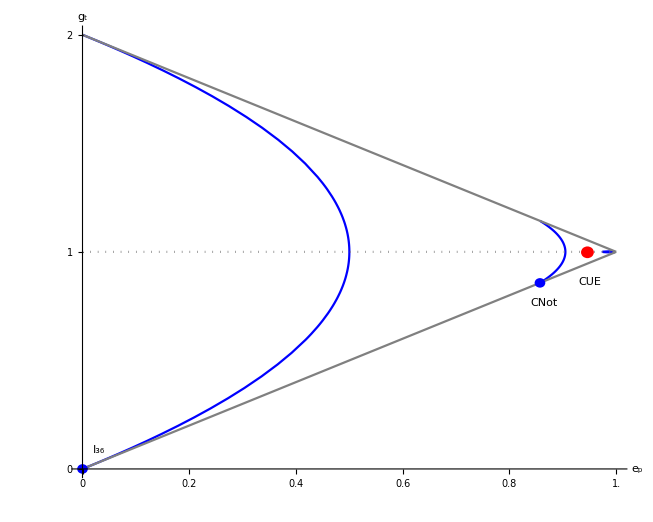

```mathematica
ParametricPlot[
{
{ep[s[P36,t]],gt[s[P36,t]]},
{ep[s[IdentityMatrix[36],t]],gt[s[IdentityMatrix[36],t]]},
{ep[s[CNot,t]],gt[s[CNot,t]]},
{t,t},
{t,-t+2},
{t,1}
},
{t,0,1},
AspectRatio->0.8,
AxesOrigin->{0.,0.},
AxesLabel->{Style["e_p",Bold,18],Style["g_t",Bold,18]},
Ticks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0},{0,1,2}},
TicksStyle->Directive[Black,18],
PlotStyle->{Blue,Blue,Blue,Gray,Gray,Directive[Dotted,Gray]},
Epilog->{
{Blue,Disk[{ep[CNot],gt[CNot]},{.01,.022}]},
{Blue,Disk[{ep[IdentityMatrix[36]],gt[IdentityMatrix[36]]},{.01,.022}]},
{Red,Disk[{ep[CUE],gt[CUE]},{.012,.027}]},
Style[Text["I_36",{0.03,0.085}],18],
Style[Text["CNot",{0.865,0.765}],18],
Style[Text["CUE",{0.95,0.86}],18]
}
]
```

### [single] cusp magnification

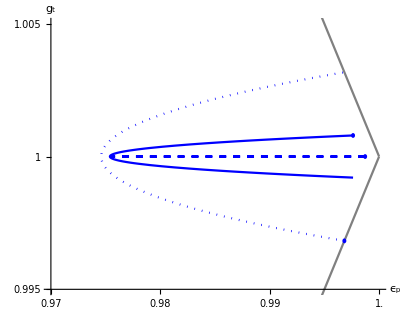

```mathematica
ParametricPlot[
{
{ep[s[P36,t]],gt[s[P36,t]]},
{ep[s[Q,t]],gt[s[Q,t]]},
{ep[s[V,t]],gt[s[V,t]]},
{(1-t)0.97+t,(1-t)0.97+t},
{(1-t)0.97+t,(1-(-t+2))0.97+(-t+2)}
},
{t,0,1},
AspectRatio->0.8,
Axes->True,
AxesLabel->{Style["e_p",Bold,16],Style["g_t",Bold,16]},
PlotRange->{{0.97,1},{0.995,1.005}},
Ticks->{{0.97,0.975,0.98,0.985,0.99,0.995,1.0},{.995,1,1.005}},
TicksStyle->Directive[Black,16],
PlotStyle->{Directive[Dotted,Blue],Blue,Directive[Dashed,Blue],Gray,Gray},
Epilog->{
{Blue,Disk[{ep[P36],gt[P36]},{.00018,.00009}]},
{Blue,Disk[{ep[Q],gt[Q]},{.00018,.00009}]},
{Blue,Disk[{ep[V],gt[V]},{.00018,.00009}]}
}
]
```

### [merged] all together

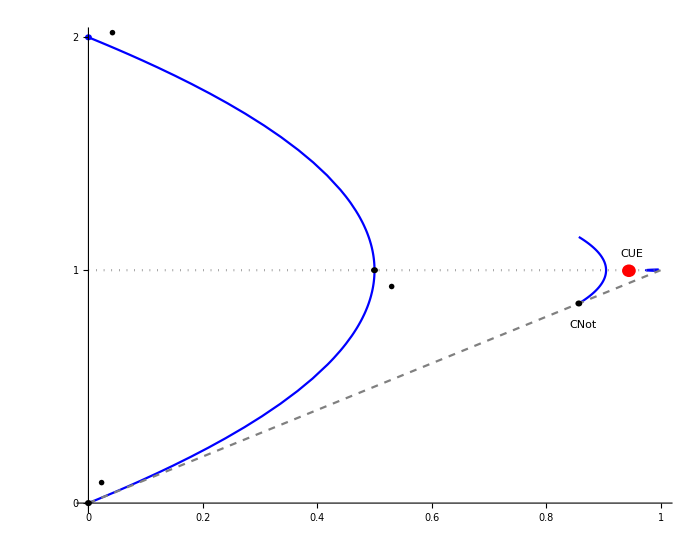

```mathematica
ParametricPlot[
{
{ep[s[P36,t]],gt[s[P36,t]]},
{ep[s[IdentityMatrix[36],t]],gt[s[IdentityMatrix[36],t]]},
{ep[s[CNot,t]],gt[s[CNot,t]]},
{t,t},
(*{t,-t+2},*)
{t,1}
},
{t,0,1},
AspectRatio->0.8,
AxesOrigin->{0.,0.},
Ticks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{0,1,2}},
BaseStyle->{FontFamily->"Latin",FontSize->22},
AxesLabel->{MaTeX["e_p",FontSize->24],MaTeX["g_t",FontSize->24]},
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
PlotStyle->{Blue,Blue,Blue,Directive[Dashed,Gray],Directive[Dotted,Gray]},
Epilog->{
{Black,Disk[{ep[CNot],gt[CNot]},{.006,.013}]},
{Black,Disk[{ep[IdentityMatrix[36]],gt[IdentityMatrix[36]]},{.006,.013}]},
{Black,Disk[{ep[N[MatrixPower[S,1/2]]],gt[N[MatrixPower[S,1/2]]]},{.006,.013}]},
{Blue,Disk[{0,2},{.006,.013}]},
{Red,Disk[{ep[CUE],gt[CUE]},{.012,.027}]},
Style[Text["CNot",{0.865,0.765}],18],
Style[Text["CUE",{0.95,1.07}],Red,18],
Style[Text[Style[MaTeX["I_{36}",FontSize->22]],{0.023,0.088}],Black,16],
Style[Text[Style[MaTeX["\sqrt{S}",FontSize->22]],{0.53,0.93}],Black,16],
Style[Text[Style[MaTeX["S",FontSize->22]],{0.042,2.02}],Black,16],
Inset[
ParametricPlot[
{
{ep[s[P36,t]],gt[s[P36,t]]},
{ep[s[Q,t]],gt[s[Q,t]]},
{ep[s[V,t]],gt[s[V,t]]},
{(1-t)0.97+t,(1-t)0.97+t},
{(1-t)0.97+t,(1-(-t+2))0.97+(-t+2)}
},
{t,0,1},
AspectRatio->0.8,
Axes->True,
(*AxesLabel->{Style["e_p",Bold,16],Style["g_t",Bold,16]},*)
PlotRange->{{0.97,1.001},{0.995,1.005}},
Ticks->{{0.97,0.98,0.99,1},{.997,1,1.003}},
TicksStyle->Directive[Black,16],
PlotStyle->{Directive[Dotted,Blue],Blue,Directive[Dashed,Blue],Directive[Dashed,Gray], Directive[Dashed,Gray]},
Epilog->{
{Black,Disk[{ep[P36],gt[P36]},{.00027,.00012}]},
{Black,Disk[{ep[Q],gt[Q]},{.00027,.00012}]},
{Black,Disk[{ep[V],gt[V]},{.00027,.00012}]},
{Red,Disk[{1,1},{.00027,.00012}]}
},
ImageSize->350],
{.75,1.7}
]
},
ImageSize->700
]
```

## (e_p,g_t)-plane for d = 3 - DATA GENERATED BY OCTAVE

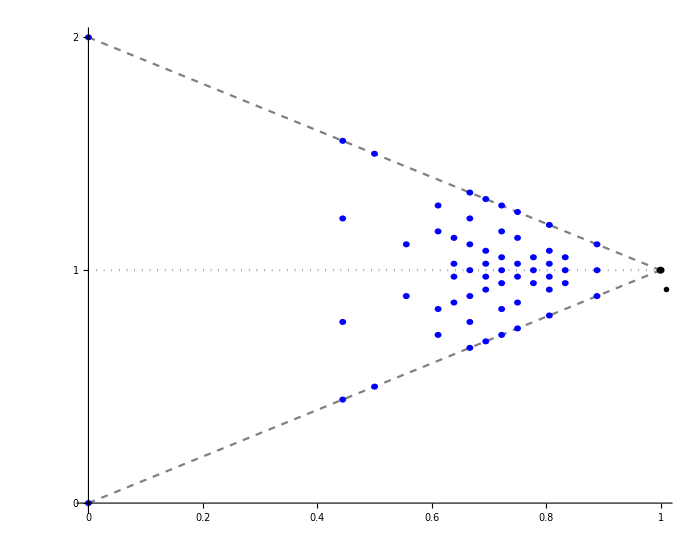

```mathematica
sx=0.006;
sy=0.013;
ParametricPlot[
{
{t,1},
{t,t},
{t,-t+2}
},
{t,0,1},
AspectRatio->0.8,
AxesOrigin->{0.,0.},
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
AxesLabel->{MaTeX["e_p",FontSize->24],MaTeX["g_t",FontSize->24]},
Ticks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{0,1,2}},
(*TicksStyle->Directive[Black,22],*)
PlotStyle->{Directive[Dotted,Gray],Directive[Dashed,Gray],Directive[Dashed,Gray]},
Epilog->{
{Blue,Disk[{0,0},{sx,sy}]},{Blue,Disk[{0,2},{sx,sy}]},{Blue,Disk[{4/9,7/9},{sx,sy}]},
{Blue,Disk[{4/9,11/9},{sx,sy}]},{Blue,Disk[{4/9,4/9},{sx,sy}]},{Blue,Disk[{4/9,14/9},{sx,sy}]},
{Blue,Disk[{0.5,0.5},{sx,sy}]},{Blue,Disk[{0.5,1.5},{sx,sy}]},{Blue,Disk[{5/9,8/9},{sx,sy}]},
{Blue,Disk[{5/9,10/9},{sx,sy}]},{Blue,Disk[{11/18,13/18},{sx,sy}]},{Blue,Disk[{11/18,5/6},{sx,sy}]},
{Blue,Disk[{11/18,7/6},{sx,sy}]},{Blue,Disk[{11/18,23/18},{sx,sy}]},{Blue,Disk[{23/36,31/36},{sx,sy}]},
{Blue,Disk[{23/36,35/36},{sx,sy}]},{Blue,Disk[{23/36,37/36},{sx,sy}]},{Blue,Disk[{23/36,41/36},{sx,sy}]},
{Blue,Disk[{2/3,2/3},{sx,sy}]},{Blue,Disk[{2/3,7/9},{sx,sy}]},{Blue,Disk[{2/3,8/9},{sx,sy}]},
{Blue,Disk[{2/3,1},{sx,sy}]},{Blue,Disk[{2/3,10/9},{sx,sy}]},{Blue,Disk[{2/3,11/9},{sx,sy}]},
{Blue,Disk[{2/3,4/3},{sx,sy}]},{Blue,Disk[{25/36,11/12},{sx,sy}]},{Blue,Disk[{25/36,35/36},{sx,sy}]},
{Blue,Disk[{25/36,37/36},{sx,sy}]},{Blue,Disk[{25/36,13/12},{sx,sy}]},{Blue,Disk[{25/36,25/36},{sx,sy}]},
{Blue,Disk[{25/36,47/36},{sx,sy}]},{Blue,Disk[{13/18,5/6},{sx,sy}]},{Blue,Disk[{13/18,17/18},{sx,sy}]},
{Blue,Disk[{13/18,19/18},{sx,sy}]},{Blue,Disk[{13/18,7/6},{sx,sy}]},{Blue,Disk[{13/18,13/18},{sx,sy}]},
{Blue,Disk[{13/18,1},{sx,sy}]},{Blue,Disk[{13/18,23/18},{sx,sy}]},{Blue,Disk[{3/4,3/4},{sx,sy}]},
{Blue,Disk[{3/4,31/36},{sx,sy}]},{Blue,Disk[{3/4,35/36},{sx,sy}]},{Blue,Disk[{3/4,37/36},{sx,sy}]},
{Blue,Disk[{3/4,41/36},{sx,sy}]},{Blue,Disk[{3/4,5/4},{sx,sy}]},{Blue,Disk[{7/9,1},{sx,sy}]},
{Blue,Disk[{7/9,17/18},{sx,sy}]},{Blue,Disk[{7/9,19/18},{sx,sy}]},{Blue,Disk[{29/36,29/36},{sx,sy}]},
{Blue,Disk[{29/36,11/12},{sx,sy}]},{Blue,Disk[{29/36,35/36},{sx,sy}]},{Blue,Disk[{29/36,37/36},{sx,sy}]},
{Blue,Disk[{29/36,13/12},{sx,sy}]},{Blue,Disk[{29/36,43/36},{sx,sy}]},{Blue,Disk[{5/6,17/18},{sx,sy}]},
{Blue,Disk[{5/6,19/18},{sx,sy}]},{Blue,Disk[{5/6,1},{sx,sy}]},{Blue,Disk[{8/9,8/9},{sx,sy}]},
{Blue,Disk[{8/9,1},{sx,sy}]},{Blue,Disk[{8/9,10/9},{sx,sy}]},{Black,Disk[{1,1},{0.007,0.015}]},
Style[Text[Style[MaTeX["T_9",FontSize->22]],{1.01,0.92}],Black,16]
},
ImageSize->700
]
```

## AME trajectory

```mathematica
trajectory={{0.99047619047457558,1.0031746031744342},{0.98888564795511913,0.99520332339690254},{0.98765490926211097,0.99662592107854719},{0.98880043028770337,0.99818909024674873},{0.98927286540953929,0.99701556864016649},{0.98937447572700155,0.99663390993576828},{0.98938220699987078,0.99747740273996333},{0.98955896607486604,0.99749364053532041},{0.98992798024980644,0.996763699051327},{0.98974072094139487,0.99737162908734944},{0.98980506392422885,0.99760675092409445},{0.99022995039886763,0.99682700943948044},{0.99004571865723623,0.99743707943363658},{0.9900786618526487,0.99762836611859063},{0.99045727055593913,0.99689925258105305},{0.9903387275599389,0.99754723973621273},{0.9903706858899608,0.9976185553407938},{0.99067871422938492,0.99698912539197249},{0.99063855037722415,0.99767668534205511},{0.99067202535823595,0.99760554493402775},{0.99091957796452146,0.99707675886421876},{0.99094638501356735,0.99783332512158174},{0.99097238483004091,0.99761361293734063},{0.9911737293585845,0.99714883955797895},{0.99124883879439674,0.99801566022195021},{0.99126142075122359,0.99765543979353577},{0.99142426163397079,0.99720906996749037},{0.99153277763407832,0.99820391594162283},{0.99153281292704154,0.99772399770849407},{0.99165673039623981,0.99726735120244547},{0.99178984703839879,0.99837454181602425},{0.99178222814455985,0.99780008707062551},{0.99185916209637037,0.9973262910634515},{0.99201276284619788,0.9985141460671989},{0.99200508198732429,0.99786577199714965},{0.99202477526245181,0.99738150631455846},{0.99219773494397101,0.99862222522690969},{0.99220033598237567,0.99791266990951677},{0.9921567516452483,0.99742766140176131},{0.99234873644142363,0.99870619065158173},{0.99237250769225627,0.99794221485963464},{0.99226566396441918,0.99746102386577018},{0.99247563223091895,0.99877518701855827},{0.99252882543604914,0.99796090818872374},{0.99236315344396853,0.99747989201828524},{0.99258923332593474,0.99883645603120774},{0.99267602154176204,0.99797565591665993},{0.99245821949865909,0.99748483484530759},{0.99269822409401387,0.99889427451918233},{0.99281895616745497,0.9979914233047138},{0.99255676425397255,0.99747859938075611},{0.99280852527329522,0.99895006995771085},{0.99296047758290085,0.99801072037137695},{0.99266250706535519,0.99746558128634188},{0.99292375868755323,0.99900294651538291},{0.99310168004036248,0.99803396214813966},{0.99277772735676018,0.99745109892090511},{0.99304574546798308,0.99905043735076293},{0.99324209266775076,0.99806004576776697},{0.99290317943976403,0.99744064891499928},{0.99317456805184445,0.99908944505214969},{0.99337972527774188,0.99808684991880836},{0.99303734963373413,0.99743912789283906},{0.99330826853778564,0.99911734896828042},{0.99351122554376614,0.99811169333964689},{0.99317585652049223,0.99744994561281808},{0.99344271436616727,0.99913311123709736},{0.99363248376838409,0.99813195658379539},{0.99331196588174597,0.99747415160931363},{0.99357229547293535,0.99913791089835224},{0.99373977029289096,0.99814593879345714},{0.99343854042244173,0.99751001161143538},{0.99369158258406109,0.99913479593482646},{0.99383102841241877,0.99815364567544951},{0.99355050242137799,0.99755349750151323},{0.99379713376100121,0.99912743308654528},{0.99390664787279182,0.99815698947265397},{0.99364629516154501,0.99759965309640064},{0.99388834899142608,0.99911875650996851},{0.99396929520416899,0.99815920805868641},{0.9937276797944905,0.99764416703026892},{0.9939670853182514,0.9991102825680036},{0.99402302430182066,0.99816390442177472},{0.99379848998366205,0.99768439651934548},{0.99403665595694912,0.99910216430747179},{0.99407228941580472,0.99817431297606718},{0.99386335128379999,0.99771958396159099},{0.99410093306176761,0.99909356561299956},{0.99412132485222671,0.99819308312199284},{0.99392689859611982,0.99775050695858458},{0.99416382926435221,0.99908298335558232},{0.99417396026890015,0.99822246691031857},{0.99399347519998127,0.99777892081955644},{0.99422907038118824,0.99906842104048121},{0.99423368916718369,0.99826463009166244},{0.99406706487986174,0.99780700879578887},{0.99430007508030993,0.99904751157052152},{0.99430376915351237,0.99832183789096918},{0.99415122718313498,0.99783689806756193},{0.99437981398470354,0.9990177489789277},{0.99438719672976261,0.99839634731642257},{0.99424891681523153,0.99787024206029429},{0.99447062287368215,0.99897696558640703},{0.9944864850584505,0.99848991032432532},{0.99436219072894128,0.99790790409081909},{0.99457404186664378,0.99892409046616182},{0.99460326654200637,0.99860290436648802},{0.99449190217807004,0.99794984145362953},{0.99469078695940083,0.99886003282403291},{0.99473783840097196,0.99873331438578883},{0.99463749734208995,0.99799529392223851},{0.9948208603836628,0.99878830574150956},{0.9948888203457682,0.99887603339921205},{0.99479693722974893,0.99804325821047912},{0.99496360570197662,0.99871491605314877},{0.99505304247310189,0.99902301262542792},{0.99496666487695862,0.99809302571046443},{0.99511745242503213,0.99864726887004573},{0.99522567712071908,0.99916449647422301},{0.99514161150902947,0.99814445447416644},{0.99527939538239263,0.99859232722717983},{0.99540061247412082,0.999291044509242},{0.99531546192422882,0.9981977910362364},{0.99544469813175307,0.99855472928583811},{0.99557113969431432,0.99939561551162537},{0.99548144536526206,0.99825318716100098},{0.99560735132900624,0.99853566338427413},{0.99573097611178474,0.99947490540632389},{0.99563359148742991,0.99831030431695256},{0.99576129771650157,0.99853292735117882},{0.99587538901785511,0.99952945468716503},{0.99576798308017511,0.998368324628228},{0.99590184797378445,0.99854198322040422},{0.99600198049187094,0.99956266159025819},{0.99588345355607766,0.99842633357128596},{0.99602659432531238,0.99855738707418995},{0.99611081610541286,0.99957934731857956},{0.9959814694843927,0.9984837474394973},{0.99613550000767903,0.99857398632421468},{0.99620393321087408,0.99958452974586964},{0.99606535180189004,0.99854049517662846},{0.99623032294875302,0.99858760655438572},{0.99628453577897513,0.99958269001541156},{0.99613924933450804,0.99859691618403257},{0.99631378090354894,0.99859527435558859},{0.99635621463163737,0.99957747938551311},{0.99620726868495346,0.99865351807438818},{0.99638881720660022,0.99859515926367903},{0.99642239635800189,0.99957170315390564},{0.99627296443160041,0.99871074412423866},{0.99645813033488295,0.99858640327740578},{0.99648606289061603,0.99956744693942934},{0.99633917756021018,0.99876881671098294},{0.99652395956034834,0.99856894428626564},{0.99654968260812771,0.99956625896862927},{0.99640809454553558,0.99882765386677275},{0.99658804476301843,0.99854338638689177},{0.99661526427264469,0.99956933183192831},{0.9964813888749664,0.9988868331394738},{0.99665168083857125,0.99851093420723236},{0.99668445970617192,0.99957764417303518},{0.99656034989166709,0.99894558506899278},{0.99671582069462605,0.99847338470559011},{0.99675867059105316,0.99959203530218443},{0.99664595779393572,0.99900281697658577},{0.99678121531568276,0.99843315426976353},{0.99683914333823198,0.99961319719317543},{0.99673891189704111,0.99905718502313134},{0.99684860286945165,0.99839330954445638},{0.99692705913692325,0.99964158121104607},{0.99683965939077712,0.99910724318902455},{0.99691896762678534,0.99835756788397201},{0.99702364315545422,0.99967723363763161},{0.99694849901893301,0.9991516959567629},{0.99699388107323772,0.99833024084431921},{0.99713032380818856,0.99971959408754507},{0.9970658330054567,0.99918975941316368},{0.99707591025083575,0.99831611443198065},{0.99724896135355134,0.99976730739280928},{0.9971925909279804,0.9992215911699962},{0.99716903330877349,0.99832028681529061},{0.99738212278083305,0.99981810091449208},{0.99733074580435765,0.99924869578570275},{0.99727894137059736,0.99834799279412079},{0.99753329726279594,0.99986876242782818},{0.99748371337048081,0.99927417251450257},{0.99741302177914748,0.99840439111008972},{0.99770682549077438,0.99991524522058117},{0.99765632084992228,0.99930265354477787},{0.99757969313867934,0.998494142769497},{0.99790718844457738,0.99995298193393867},{0.99785398937589553,0.99933975893978766},{0.99778662720660583,0.99862041319392758},{0.99813727270541452,0.9999776204239047},{0.9980808346303065,0.99939087112697711},{0.9980374778311234,0.99878291976229505},{0.99839555514377931,0.99998643280444044},{0.998336710776488,0.99945916231666032},{0.99832756586339721,0.99897525911061191},{0.99867314746983604,0.99998019640308999},{0.99861409022305248,0.99954338064667314},{0.99864079319198007,0.99918317270571244},{0.99895301448374241,0.99996428057217834},{0.99889693280032588,0.99963681749887701},{0.99895138851379994,0.9993864325860109},{0.99921365828440134,0.99994715536210677},{0.9991638591324421,0.99972900192491898},{0.99923183084109146,0.9995651688653806},{0.99943642827432555,0.99993636873879466},{0.9993952300661797,0.9998098200261426},{0.99946270611817933,0.99970702973188896},{0.99961178269721662,0.99993501104701077},{0.99957986001537646,0.99987334843189313},{0.99963778148700477,0.99980998363811635},{0.9997404109790593,0.99994151466628944},{0.99971696267527066,0.99991887379542543},{0.99976203448557999,0.99987966771512715},{0.999829770934757,0.99995213316067866},{0.99981320128675999,0.99994925105644672},{0.99984605316624275,0.9999246377145018},{0.99988955349177178,0.9999634440742482},{0.99987813260383618,0.99996855214359448},{0.99990109290697915,0.99995287406211197},{0.99992862923613934,0.99997341614695689},{0.99992086772541455,0.99998047707626492},{0.999936507474946,0.99997039992644876},{0.99995386183465662,0.99998130449138911},{0.99994862380669525,0.99998776862137539},{0.9999591201711695,0.99998126915080987},{0.99997008404960619,0.99998713891724889},{0.99996655923160827,0.99999223925933356},{0.99997354860074861,0.99998804675955533},{0.99998051961992163,0.9999912748542229},{0.99997814994140599,0.9999950106179063},{0.99998278760957726,0.99999230866217803},{0.99998725607068328,0.99999412988837599},{0.99998566340854111,0.99999675423625656},{0.99998873755694451,0.99999501370336341},{0.99999162583237156,0.99999606907538885},{0.99999055557883043,0.9999978681162569},{0.99999259410315666,0.99999674623123913},{0.99999447531995322,0.99999737382140275},{0.99999375629534892,0.99999858945918263},{0.99999510950492687,0.99999786506798394},{0.99999634283769701,0.99999824716983876},{0.9999958599386003,0.99999906179440678},{0.9999967593963679,0.99999859280846748},{0.99999757230644626,0.99999883027245218},{0.99999724811039448,0.99999937368624037},{0.99999784675628867,0.99999906905679614},{0.99999838482766457,0.9999992192012036},{0.99999816725559754,0.99999958088241914},{0.99999856617878269,0.99999938230272034},{0.99999892349732589,0.99999947858186677},{0.99999877752762711,0.99999971910187657},{0.99999904364582148,0.99999958918639142},{0.99999928152137629,0.99999965161976123}};
SEED={{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
SEED2={{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
SEED3={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

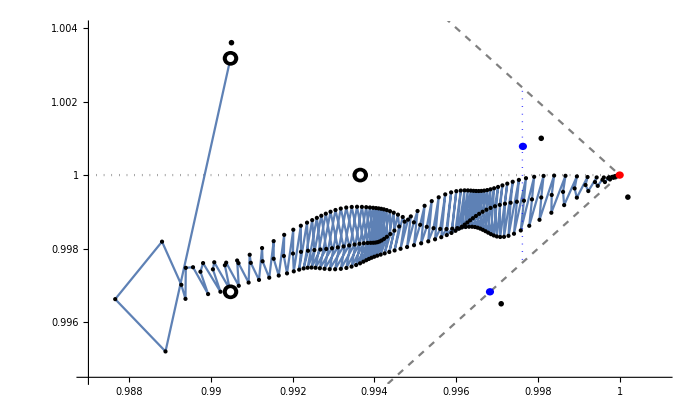

```mathematica
xx=0.987;
p1=ParametricPlot[
{
{(1-t)xx+t,(1-t)xx+t},
{(1-t)xx+t,(1-(-t+2))xx+(-t+2)},
{(1-t) xx+t,1}
},
{t,0,1},
AspectRatio->0.60,
PlotRange->{{xx,1.001},{0.9945,1.004}},
Ticks->{{0.988,0.99,0.992,0.994,0.996,0.998,1},{.996,.998,1,1.002,1.004}},
BaseStyle->{FontFamily->"Latin",FontSize->22},
AxesLabel->{MaTeX["e_p",FontSize->24],MaTeX["g_t",FontSize->24]},
TicksStyle->{{FontFamily->"Times New Roman",FontSize->20},{FontFamily->"Times New Roman",FontSize->20}},
PlotStyle->{Directive[Dashed,Gray],Directive[Dashed,Gray],Directive[Dotted,Gray]},
Epilog->{
{Blue,Disk[{ep[P36],gt[P36]},{.0001,.0001}]},
{Red,Disk[{1,1},{.0001,.0001}]},
{Black,Disk[{ep[SEED],gt[SEED]},{.00019,.0002}]},
{White,Disk[{ep[SEED],gt[SEED]},{.00009,.0001}]},
{Black,Disk[{ep[SEED2],gt[SEED2]},{.00019,.0002}]},
{White,Disk[{ep[SEED2],gt[SEED2]},{.00009,.0001}]},
{Black,Disk[{ep[SEED3],gt[SEED3]},{.00019,.0002}]},
{White,Disk[{ep[SEED3],gt[SEED3]},{.00009,.0001}]},
Style[Text[Style[MaTeX["P^{\star}",FontSize->22]],{0.9905,1.0036}],Black,16],
Style[Text[Style[MaTeX["P",FontSize->22]],{0.9971,0.9965}],Black,16],
Style[Text[Style[MaTeX["T_{36}",FontSize->22]],{1.0002,0.9994}],Black,16],
{Thick,Blue,Dotted,Line[{{ep[Q],0.9977},{ep[Q],1.0024}}]},
{Blue,Disk[{ep[Q],gt[Q]},{.0001,.0001}]},
Style[Text[Style[MaTeX["Q^{\star}",FontSize->22]],{0.99808,1.001}],Black,16]
}
];
p2=ListPlot[trajectory,Joined->True,Mesh->All,MeshStyle->{Directive[PointSize[Medium]],Black}];
Show[p1,p2,ImageSize->700]
```